```mathematica
Quit[]
```

## Functions and Graph Generators

```mathematica
<<"HelicityVariables`"
<<"GraphGenerator`"
```

### Independent Spin Structures

```mathematica
Options[IndependentSpinStructres]={"MomentumConservation"->True,"MassSquared"->False};

IndependentSpinStructres[dim_Integer,OptionsPattern[]][list__?((Length[#]==2 && IntegerQ[2*#[[2]]])||(Length[#]==3 && IntegerQ[2*#[[2]]] && IntegerQ[2*#[[3]]] && #[[2]]>=Abs[#[[3]]])&)]:=
Module[
{
massivespins=Table[If[Length[i]==2(*if massless*),0,i[[2]]],{i,{list}}],(*a list of all the spins, for massless particles is zero*)
x= Table[If[Length[i]==2,0,i[[3]]],{i,{list}}], (*a list of all the transversality, for massless particles is zero*)
momenta=dim-Sum[i[[2]],{i,{list}}], (*the number of momenta insertions in the structures*)
n=Length[{list}]
},

If[momenta<0,{}];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins]; (*all the possible transversality combinations for the spins*)
massivespins={Abs[#-x],#}&/@massivespins; (*for each transversality configuration gives the difference (in absolute value, it does not distinguish between m and OverTilde[m])*)
massivespins={
Product[Mass[{list}[[i,1]]]^#[[1,i]],{i,n}],(*the masses to compensate the mass dimensions*)
Total@#[[1]],(*the total difference*)
Table[If[Length[{list}[[i]]]==2,{list}[[i]],{{list}[[i,1]],{list}[[i,2]],#[[2,i]]}],{i,n}](*if massive, changes the original transversalities in all their possible combinations*)
}&/@massivespins;

massivespins=SortBy[massivespins,#[[1]]&];

massivespins=#[[1]]*UniformMassStructres[dim-#[[2]],"MomentumConservation"->OptionValue["MomentumConservation"]][Sequence@@#[[3]]]&/@massivespins; (*applies the algorithm with uniform mass powers*)

(*ITERATIVE ALGORTHM!*)
If[momenta-2>=0&&OptionValue["MassSquared"], (*if we want to consider terms proportional to M^2*)
x=Table[If[Length[i]==2,Nothing,Mass[i[[1]]]^2],{i,{list}}]; (*we consider a SINGLE insertion of M^2 for any massive particle*)
massivespins=(*add the structures to those already found*)
Join[
massivespins,
Times@@@Tuples[{x,Flatten@IndependentSpinStructres[dim-2(*two momentum insertions*),"MomentumConservation"->OptionValue["MomentumConservation"],"MassSquared"->OptionValue["MassSquared"]][list]}] (*all the possible combinations of single M^2 with structures with lower mass dimensions*)
];
];

Return[Flatten@massivespins]

]
```

### Uniform Mass Structures

```mathematica
Options[UniformMassStructres]={"MomentumConservation"->True,"Echos"->False};

UniformMassStructres[dim_Integer,OptionsPattern[]][list__]:=
Module[{labels=Part[#,1]&/@{list},spins=Delete[#,1]&/@{list},angles,squares,structures},

{angles,squares}=
Transpose[(*gives the number of angles and the number of squares for each particle*)
If[Length[#]==1(*if massless*),
{Abs[#[[1]]]-#[[1]],Abs[#[[1]]]+#[[1]]},
{#[[1]]-#[[2]],#[[1]]+#[[2]]}(*the definition of transversality for massive particles*)
]&/@spins
];

If[
TrueQ@OptionValue["MomentumConservation"],(*structures given the possible distributions of momentum insertions*)
structures=(Append[#,0]&/@PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]-1]),(*if we consider structures modulo momentum conservation, we can ignore the momentum of the nth-particle*)
structures=PermutationsOfPartitions[dim-Total[angles]/2-Total[squares]/2,Length[angles]]
];

structures={{angles+#,squares+#},#}&/@structures;(*each momentum add an angle and a square*)

structures=If[Length[#[[1]]]<2(*IsLoopLessDoable returns Nothing if no graph is possible*),Nothing,#]&/@(MapAt[Map[IsLoopLessDoable,#,{1}]&,#,1]&/@structures)(*we check if a loop-less graph can be done for both angles and squares*);

structures=SpinStructures[#,labels,Length/@spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@structures;

structures=Flatten[structures,1];

Return[(*Flatten@*)structures]

]
```

### Auxiliary functions

#### Spin Structures

```mathematica
Options[SpinStructures]={"MomentumConservation"->True,"Echos"->False,"GraphOnly"->False};

SpinStructures[{{anglestructure_List,squarestructure_List},momenta_List},labels_List,spins_List(*1 or 2 if the corresponding particle is massless or massive, respectively*),OptionsPattern[]]:=
Module[{formfactors,angles,squares},

angles=AllNonIntersectingGraphs[anglestructure];
squares=AllNonIntersectingGraphs[squarestructure];

formfactors=Tuples[{angles,squares}];

If[OptionValue["Echos"], (*Printing intermediate sterps*)
Echo[momenta,"Momenta:"];
Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs before momentum conservation:"]; (*Draw all the structures, without distinguishing between free massive spinors and momenta*)
If[MemberQ[spins,2],Echo[FreeSpinorsAndMomenta[#,momenta,labels,spins]&/@formfactors,"Graphs with momenta:"]] (*if there is a massive particle, draw the corresponding graph with free spinors and momenta*)
];

If[
OptionValue["MomentumConservation"],
formfactors=PlanarMomentumConservation[#,momenta,"Echos"->OptionValue["Echos"]]&/@formfactors;

If[momenta[[1]]!=0&&anglestructure[[-1]]!=0&&squarestructure[[-1]]!=0,

(*squares={};
angles={};*)

(*THE FIRST ALGORITHM GIVES TOO MANY CONSTRAINTS!*)
(*If[anglestructure[[-2]]!=0,
angles=If[Length[#]==2,Tuples[AllNonIntersectingGraphs/@#],{}]&@(IsLoopLessDoable/@{MapAt[(#-1)&,anglestructure,{{1},{-2}}],MapAt[(#-1)&,squarestructure,{{1},{-1}}]})
];
If[squarestructure[[-2]]!=0,
squares=If[Length[#]==2,Tuples[AllNonIntersectingGraphs/@#],{}]&@(IsLoopLessDoable/@{MapAt[(#-1)&,anglestructure,{{1},{-1}}],MapAt[(#-1)&,squarestructure,{{1},{-2}}]})
];

angles=PlanarMomentumConservation[#,MapAt[(#-1)&,momenta,{1}]]&/@Join[angles,squares];*)

(*THE SECOND ALGORITHM DOES NOT GIVE ALL THE CONSTRAINTS!*)
(*If[anglestructure[[-2]]!=0,
angles=
If[Length[#]==2, (*if both angles and squares passed the IsLoopLessDoable test*)
SpinStructures[ (*ITERATIVE ALGORITHM!*)
{#,
MapAt[(#-1)&,momenta,{1}] (*we need to remove one insertion of momentum 1*)
},
labels,
spins,
"GraphOnly"->True], (*The spinor polynomial are not needed*)
{}
]&@
Echo[#,ToString[MapAt[(#-1)&,momenta,{1}]]]&@(
IsLoopLessDoable/@(*we need to check if drawing graphs is even possible*)
{
MapAt[(#-1)&,anglestructure,{{1},{-2}}],(*removing a red edge connecting the vertices 1 and (n-1)*)
MapAt[(#-1)&,squarestructure,{{1},{-1}}] (*removing a blue edge connecting the vertices 1 and (n)*)
}
)
];
If[squarestructure[[-2]]!=0, (*same inverting blue and red edges*)
squares=If[Length[#]==2,SpinStructures[{#,MapAt[(#-1)&,momenta,{1}]},labels,spins,"GraphOnly"->True],{}]&@Echo[#,ToString[MapAt[(#-1)&,momenta,{1}]]]&@(IsLoopLessDoable/@{MapAt[(#-1)&,anglestructure,{{1},{-1}}],MapAt[(#-1)&,squarestructure,{{1},{-2}}]})
];

angles=Map[#+({SparseArray[{{1,#-1}->1},{#,#}],SparseArray[{{1,#}->1},{#,#}]}&@Length[spins])&,angles,{1}];
squares=Map[#+({SparseArray[{{1,#}->1},{#,#}],SparseArray[{{1,#-1}->1},{#,#}]}&@Length[spins])&,squares,{1}];*)

squares=Length[spins];
angles=
Flatten[
Permutations/@Flatten[
Table[
({Join[PadRight[{i},squares-2],#],Join[PadRight[{i},squares-2],Reverse@#]})&/@(PadRight[#,2]&/@IntegerPartitions[i,2]),
{i,3}],
1],
1];
angles=({anglestructure,squarestructure}-#)&/@angles;
angles=If[MemberQ[Flatten[#],_?(#<0&)],Nothing,#]&/@angles;
angles=Map[IsLoopLessDoable,angles,{2}];
angles=If[Length[#]==2,ExtraGraphs[#,{anglestructure,squarestructure}-#,momenta,labels,spins,squares],Nothing]&/@angles;
angles=Flatten[angles,1];

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra momentum conservatin:"](*;
Echo[DrawStructure[#,labels]&/@squares,"Extra momentum conservatin 2:"];*)
];

angles=IndependentConstrainQ/@angles;
(*squares=IndependentConstrainQ/@squares;*)

If[OptionValue["Echos"],
Echo[DrawStructure[#,labels]&/@angles,"Extra momentum conservatin:"](*;
Echo[DrawStructure[#,labels]&/@squares,"Extra momentum conservatin 2:"];*)
];

formfactors=ExtraMomentumConservation[formfactors,Length[Join[angles(*,squares*)]]];
]
];

If[OptionValue["Echos"],
If[¬MatchQ[formfactors,{}],Echo[Map[DrawStructure[#,labels]&,formfactors,{1}],"Graphs:"],Echo["No graph survided."]] (*Draw the graph which survived momentum conservation*)
];

If[¬OptionValue["GraphOnly"],
formfactors=FromMatrixToSpinors[#,momenta,labels,spins,"MomentumConservation"->OptionValue["MomentumConservation"],"Echos"->OptionValue["Echos"]]&/@formfactors;
];

Return[formfactors];
]
```

```mathematica
Flatten[Permutations/@Flatten[Table[({Join[PadRight[{i},4-2],#],Join[PadRight[{i},4-2],Reverse@#]})&/@(PadRight[#,2]&/@IntegerPartitions[i,2]),{i,3}],1],1]
```

{{{1,0,1,0},{1,0,0,1}},{{1,0,0,1},{1,0,1,0}},{{2,0,2,0},{2,0,0,2}},{{2,0,0,2},{2,0,2,0}},{{2,0,1,1},{2,0,1,1}},{{3,0,3,0},{3,0,0,3}},{{3,0,0,3},{3,0,3,0}},{{3,0,2,1},{3,0,1,2}},{{3,0,1,2},{3,0,2,1}}}

```mathematica
SparseArray[Table[{1,i}->#[[i]],{i,2,4}],{4,4}]&@{2,0,2,1}
```

SparseArray[…]

#### Splitting Free Spinors and Momenta

```mathematica
FreeSpinorsAndMomenta[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List]:=
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]; (*if the vertex is massive, we made the label appear (d+1) times, where d is the number of its momentum insertions. If it is massless, it must appear only once*)
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];(*given {1,...m} where m is the number of particles + the number of massive momentum insertions, it splits this list into sublist each corresponding to free spinor + momenta for massive particles and massless vertex*)
forbiddenEdges=Flatten[
Map[
Subsets[#,{2}]&,
If[Length[#]<2,Nothing(*excluding massless vertices and massive states with no momentum insertions*),#]&/@positions,
{1}
],
1];(*the list of edges which connect a momentum vertex with the corresponding free spinor vertex*)

nonmomenta =Part[#,1]&/@positions;

n=Length[Flatten@newlabels];

newangles=
SparseArray[
MapAt[
ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,(*change the labels with the position of free spinor vertices*)
#,
{1}(*ArrayRules gives {non-zero position -> non-zero value}, and we should act only on the positions*)
]&/@ArrayRules[adjAngle],{n,n}(*the dimension of the array must be specified*)];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[
Join[
Sort[Select[#,MatchQ[#,{n,_}]&]],
Sort[Select[#,MatchQ[#,{_,n}]&]]
]&@newangles["NonzeroPositions"],
1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};(*checks if the algorithm above did a good job!*)

newlabels=Flatten@newlabels;

DrawStructure[{newangles,newsquares},newlabels]

]
```

```mathematica
Planarise[matrix_,forbiddenEdges_]:=
Module[{x=matrix},
While[
IsGraphNonIntesercting[x]==Nothing,
Print["OPS! If you are not Stefano, please ignore!"];
x=(If[IntersectingQ[#["NonzeroPositions"],forbiddenEdges],Nothing,#]&/@SchoutenCrossing[x]);
x=Part[x,1]
];
Return[x]
]
```

#### Planar Momentum Conservation

```mathematica
Options[PlanarMomentumConservation]={"Echos"->False};

PlanarMomentumConservation[{angles_,squares_},momenta_List,OptionsPattern[]]:=
Module[{nonzeroangles=angles["NonzeroPositions"],nonzerosquares=squares["NonzeroPositions"],forbidden={},n=Length[momenta]},

If[momenta[[-2]]!=0,
AppendTo[forbidden,MemberQ[nonzeroangles,{n-1,n}]||MemberQ[nonzerosquares,{n-1,n}]]
];

If[
momenta[[1]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n-1}](*,
MemberQ[nonzeroangles,{n-1,n}]&&MemberQ[nonzerosquares,{1,n}],
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{n-1,n}]*)(*,
MemberQ[nonzeroangles,{1,n}]&&MemberQ[nonzerosquares,{1,n}]*)
}
];
If[
momenta[[-2]]!=0,
forbidden=
Join[
forbidden,
{
MemberQ[nonzeroangles,{1,n-1}]&&MemberQ[nonzerosquares,{1,n-1}]
}
]
]
];

If[If[OptionValue["Echos"],Echo[Or@@Echo[forbidden,"Conditions:"]],Or@@forbidden],Return[Nothing],Return[{angles,squares}]]
]
```

```mathematica
ReinstateFirst[list_List,squares_Integer]:=SparseArray[Table[{1,i}->list[[i]],{i,2,squares}],{squares,squares}]

ExtraGraphs[angles_List,valencies_List,momenta_List,labels_List,spins_List,n_Integer]:=(#+(ReinstateFirst[#,n]&/@valencies))&/@SpinStructures[{angles,MapAt[(#-valencies[[1,1]])&,momenta,{1}]},labels,spins,"GraphOnly"->True];

IndependentConstrainQ[{angles_SparseArray,squares_SparseArray}]:=If[MatchQ[IsGraphNonIntesercting[angles],Nothing]||MatchQ[IsGraphNonIntesercting[squares],Nothing],{angles,squares},Nothing]

ExtraMomentumConservation[formfactors_List,n_Integer]:=DeleteCases[formfactors,_?(ExtraCondition[#]&),1,n]

ExtraCondition[formfactor_List]:=(formfactor[[1,-2,-1]]!=0&&formfactor[[2,1,-1]]!=0)||(formfactor[[2,-2,-1]]!=0&&formfactor[[1,1,-1]]!=0)||(formfactor[[1,1,-1]]!=0&&formfactor[[2,1,-1]]!=0)
```

#### From Matrix to Spinors structures

```mathematica
Options[FromMatrixToSpinors]={"MomentumConservation"->True,"Echos"->True};

FromMatrixToSpinors[{adjAngle_,adjSquare_},momenta_List,labels_List,spins_List,OptionsPattern[]]:=
If[MemberQ[spins,2],
Module[{newlabels,types,positions,nonmomenta,newangles,newsquares,n,forbiddenEdges},

(*Echo[{{adjAngle,adjSquare},momenta}];*)

newlabels=If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}];
positions=FoldPairList[TakeDrop,Range@Length[Flatten@newlabels],Length/@newlabels];
forbiddenEdges=Flatten[Map[Subsets[#,{2}]&,If[Length[#]<2,Nothing,#]&/@positions,{1}],1];

nonmomenta =(* Table[1+Sum[Length[newlabels[[i]]],{i,1,j-1}],{j,1,Length@momenta}]*)Part[#,1]&/@positions;

(*newlabels=Flatten[newlabels];*)
n=Length[Flatten@newlabels];

newangles=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjAngle],{n,n}];
newsquares=SparseArray[MapAt[ReplaceAll[#,Thread[Rule[Range@Length[labels],nonmomenta]]]&,#,{1}]&/@ArrayRules[adjSquare],{n,n}];

(*newlabels=Flatten[newlabels];*)
(*Echo[{newangles,newsquares}];*)

Do[
n=i[[-1]];
Do[
{newangles[[Sequence@@#]]--,newangles[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newangles["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newangles["NonzeroPositions"],1];
{newsquares[[Sequence@@#]]--,newsquares[[Sequence@@ReplaceAll[#,{n->j}]]]++}&@(*Part[Sort[Select[newsquares["NonzeroPositions"],MatchQ[#,{n,_}|{_,n}]&]],1]*)
Part[Join[Sort[Select[#,MatchQ[#,{n,_}]&]],Sort[Select[#,MatchQ[#,{_,n}]&]]]&@newsquares["NonzeroPositions"],1],
{j,Delete[i,-1]}
],
{i,Reverse/@positions}
];

{newangles,newsquares}=Planarise[#,forbiddenEdges]&/@{newangles,newsquares};

types=Flatten@Table[If[spins[[i]]==1,1,{2,ConstantArray[3,momenta[[i]]]}],{i,Length@positions}];
newlabels=Flatten@newlabels;

(*If[OptionValue["Echos"],Echo[DrawStructure[{newangles,newsquares},newlabels],"New graph:"]];*)

(*If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{newangles,newsquares},positions,spins],Return[Nothing]]
];*)

Return[(*{newangles,newsquares}*)
Times@@((AngleB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$up][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$up][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newangles],-1])*
Times@@((SquareB[
If[types[[#[[1,1]]]]==1,SpinorML[newlabels[[#[[1,1]]]]],If[types[[#[[1,1]]]]==2,SpinorMV[][newlabels[[#[[1,1]]]]],SpinorMV[$down][newlabels[[#[[1,1]]]],StringJoin["I",ToString[newlabels[[#[[1,1]]]]],ToString[#[[1,1]]]]]]],
If[types[[#[[1,2]]]]==1,SpinorML[newlabels[[#[[1,2]]]]],If[types[[#[[1,2]]]]==2,SpinorMV[][newlabels[[#[[1,2]]]]],SpinorMV[$down][newlabels[[#[[1,2]]]],StringJoin["I",ToString[newlabels[[#[[1,2]]]]],ToString[#[[1,2]]]]]]]]^#[[2]]
)&/@Delete[ArrayRules[newsquares],-1])
]

]
,

If[
TrueQ@OptionValue["MomentumConservation"],
If[PlanarMomentumConservation[{adjAngle,adjSquare},FoldPairList[TakeDrop,Range@Length[Flatten@#],Length/@#],spins]&@(If[#[[3]]==2,ConstantArray[#[[1]],#[[2]]+1],{#[[1]]}]&/@Transpose[{labels,momenta,spins}]),Return[Nothing]]
];

Times@@(AngleB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjAngle["NonzeroPositions"],adjAngle["NonzeroValues"]}])*Times@@(SquareB[SpinorML[labels[[#[[1,1]]]]],SpinorML[labels[[#[[1,2]]]]]]^#[[2]]&/@Transpose[{adjSquare["NonzeroPositions"],adjSquare["NonzeroValues"]}])
]
```

#### Draw Structures

```mathematica
DrawStructure[{adjacencyAngle_,adjacencySquare_},labels_List]:=Show[{DrawAdjacencyGraph[adjacencyAngle,"Colour"->Red],DrawAdjacencyGraph[adjacencySquare,"Colour"->Blue,"Labels"->labels]}]
```

## Examples

```mathematica
UniformMassStructres[14,"MomentumConservation"->True][{a,5,2},{b,5,2},{c,2},{d,-2}]
```

{da^2 db^2 ab ca^2 cb^2 ab^5}

```mathematica
UniformMassStructres[3,"MomentumConservation"->True][{1,1/2},{2,1/2},{3,0},{4,0},{5,0}]
```

{12 12^2,13 12 13,23 12 23,24 12 24,34 12 34,34 14 23}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
IndependentSpinStructres[6,"MomentumConservation"->True,"MassSquared"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
Complement[%,%%]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 43p_2 1 31 12,-42 12 43p_2 2 31,-41 43p_2 2 32 12,41^2 1 2 32^2,42^2 1 2 31^2}

{12 (43p_2)^2 12,-41 42 33p_2 31 32,-41 12 43p_2 1 32,-42 43p_2 1 31 12,-42 12 43p_2 2 31,-41 43p_2 2 32 12,41^2 1 2 32^2,42^2 1 2 31^2,41 42 1^2 31 32,41 42 2^2 31 32}

{41 42 1^2 31 32,41 42 2^2 31 32}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,1},{4,-1}]
```

{12 (43p_2)^2 12,-41 42 33p_2 31 32}

```mathematica
Length/@(UniformMassStructres[12,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,1,0},{3,1},{4,-1}}]))
(Permutations[{{1,1,0},{2,1,0},{3,1},{4,-1}}]);
{%[[#]],%%[[#]]}&@-9
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

{{{3,1},{2,1,0},{4,-1},{1,1,0}},5}

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1,0},{3,-1},{4,1,0}]
```

{-24 31p_2 34p_2 12,12 34 31p_2 12 14}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
%//Length
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 2I242I24p_3 41 12,-12 12p_3 33p_2 2I232I23p_3 41^2}

4

```mathematica
IndependentSpinStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
```

{-(11p_2)^2 22p_1 34p_2 43,14p_2 11p_2 22p_1 33p_2 41,-12 14p_2 33p_2 2I242I24p_3 41 12,-12 12p_3 33p_2 2I232I23p_3 41^2,-12 (14p_2)^2 33p_2 1 12,-13 14p_2 11p_2 22p_1 1 43,-11p_3p_2 12 33p_2 1 41 42,11p_2 22p_1 31p_2 1 41 43,-11p_2 22p_1 33p_2 1 41^2,12 33p_2 2I232I23p_3 1 41^2 12,-11p_3 22p_3 33p_2 1 41^2,-12 13 14p_2 13p_2 1^2 42,-22p_1 31p_2 1^2 41^2 13,21p_3 33p_2 1^2 41^2 12,12p_2p_1 12 33p_2 2 41^2,-12p_2p_1 12 31p_2 2 41 43,12^2 33p_2 2I232I23p_3 2 41^2,-(14p_2)^2 33p_2 2 12^2,13 14p_2 2 43 12 12p_2p_1,-11p_3p_2 33p_2 2 41 42 12,-(12p_3)^2 33p_2 2 41^2,-12^2 11p_2 34p_2 1 2 43,12^2 14p_2 33p_2 1 2 41,-13 14p_2 13p_2 1 2 42 12,-13 13p_2 12p_3 1 2 41 42,-23p_1p_2 12 1 2 41^2 13,12 21p_3 33p_2 1 2 41^2,-11p_2 34p_2 1 2 43 12^2,14p_2 33p_2 1 2 41 12^2,12p_3 33p_2 1 2 41^2 12,-12^2 13 14p_2 1^2 2 43,-23 21p_3 1^2 2 41^2 13,31p_2 1^2 2 41 43 12^2,-33p_2 1^2 2 41^2 12^2,-12 11p_2 (34p_2)^2 3 12,-13p_3p_2 12 34p_2 3 41 12,13p_3p_2 23 12p_3 3 41^2,-(11p_2)^2 22p_1 3 43^2,-(13p_2)^2 22p_1 3 41^2,11p_2 13p_2 22p_1 3 41 43,-12 13p_2 3 41^2 23p_3p_2,-12 13 14p_2 34p_2 1 3 12,-13p_3p_2 12 13 1 3 41 42,12 (13p_2)^2 1 3 41 42,-12 14p_2 13p_2 1 3 43 12,12 34p_2 31p_2 1 3 41 12,-13p_3p_2 23 1 3 41^2 12,11p_2 22p_1 1 3 41 43 13,-13p_2 22p_1 1 3 41^2 13,-12 1 3 41^2 23 13p_3p_2,-12 13^2 14p_2 1^2 3 42,23 31p_2 1^2 3 41^2 12,-22p_1 1^2 3 41^2 13^2,-21p_3 1^2 3 41^2 13 23,12^2 34p_2 31p_2 2 3 41,-13p_3p_2 12 23 2 3 41^2,-12 13p_2 23p_1 2 3 41^2,-12p_2p_1 12 2 3 41 43 13,-13 14p_2 34p_2 2 3 12^2,-13p_3p_2 13 2 3 41 42 12,-14p_2 13p_2 2 3 43 12^2,(13p_2)^2 2 3 41 42 12,-13p_2 12p_3 2 3 41^2 23,12^2 13 34p_2 1 2 3 41,-12^2 11p_2 1 2 3 43^2,12^2 13p_2 1 2 3 41 43,-13^2 14p_2 1 2 3 42 12,-13^2 12p_3 1 2 3 41 42,12 23 31p_2 1 2 3 41^2,-23^2 11p_3 1 2 3 41^2,-12 23p_1 1 2 3 41^2 13,13 34p_2 1 2 3 41 12^2,-11p_2 1 2 3 43^2 12^2,13p_2 1 2 3 41^2 12 23,13p_2 1 2 3 41 43 12^2,-11p_3 1 2 3 41^2 23^2,1^2 2 3 41 43 12^2 13,1^2 2 3 41^2 12 13 23}

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{4,1},{3,1,0},{1,2,0},{2,1,0}]//Length
```

5

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]
```

{-12 11p_2 34p_2 43 12,12 14p_2 33p_2 41 12,12 12p_3 33p_2 41^2}

{-24 34p_2 41p_2 12 34,24 33p_2 44p_2 12 14,-14 24 33p_2 12 14^2}

```mathematica
IndependentSpinStructres[17,"MomentumConservation"->True][{4,2,0},{3,1,0},{2,1,0},{1,1}]//Length
IndependentSpinStructres[17,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

258

258

```mathematica
list={{1,1},{2,1,0},{3,1,0},{4,2,0}}

massivespins=Table[If[Length[i]==2(*if massless*),0,i[[2]]],{i,list}];(*a list of all the spins, for massless particles is zero*)
x= Table[If[Length[i]==2,0,i[[3]]],{i,list}]; (*a list of all the transversality, for massless particles is zero*)
momenta=9-Sum[i[[2]],{i,list}]; (*the number of momenta insertions in the structures*)
n=Length[list];

massivespins=Tuples[(Range[-#,#,1])&/@massivespins]; (*all the possible transversality combinations for the spins*)
massivespins={Abs[#-x],#}&/@massivespins;(*for each transversality configuration gives the difference (in absolute value, it does not distinguish between m and OverTilde[m])*)
massivespins={
(*Product[Mass[list[[i,1]]]^#[[1,i]],{i,n}],*)(*the masses to compensate the mass dimensions*)
Total@#[[1]],(*the total difference*)
Table[If[Length[list[[i]]]==2,list[[i]],{list[[i,1]],list[[i,2]],#[[2,i]]}],{i,n}](*if massive, changes the original transversalities in all their possible combinations*)
}&/@massivespins
If[Length[UniformMassStructres[9-#[[1]]][Sequence@@#[[2]]]]==Length[UniformMassStructres[9-#[[1]]][Sequence@@Reverse@#[[2]]]],Nothing,#]&/@massivespins
```

{{1,1},{2,1,0},{3,1,0},{4,2,0}}

{{4,{{1,1},{2,1,-1},{3,1,-1},{4,2,-2}}},{3,{{1,1},{2,1,-1},{3,1,-1},{4,2,-1}}},{2,{{1,1},{2,1,-1},{3,1,-1},{4,2,0}}},{3,{{1,1},{2,1,-1},{3,1,-1},{4,2,1}}},{4,{{1,1},{2,1,-1},{3,1,-1},{4,2,2}}},{3,{{1,1},{2,1,-1},{3,1,0},{4,2,-2}}},{2,{{1,1},{2,1,-1},{3,1,0},{4,2,-1}}},{1,{{1,1},{2,1,-1},{3,1,0},{4,2,0}}},{2,{{1,1},{2,1,-1},{3,1,0},{4,2,1}}},{3,{{1,1},{2,1,-1},{3,1,0},{4,2,2}}},{4,{{1,1},{2,1,-1},{3,1,1},{4,2,-2}}},{3,{{1,1},{2,1,-1},{3,1,1},{4,2,-1}}},{2,{{1,1},{2,1,-1},{3,1,1},{4,2,0}}},{3,{{1,1},{2,1,-1},{3,1,1},{4,2,1}}},{4,{{1,1},{2,1,-1},{3,1,1},{4,2,2}}},{3,{{1,1},{2,1,0},{3,1,-1},{4,2,-2}}},{2,{{1,1},{2,1,0},{3,1,-1},{4,2,-1}}},{1,{{1,1},{2,1,0},{3,1,-1},{4,2,0}}},{2,{{1,1},{2,1,0},{3,1,-1},{4,2,1}}},{3,{{1,1},{2,1,0},{3,1,-1},{4,2,2}}},{2,{{1,1},{2,1,0},{3,1,0},{4,2,-2}}},{1,{{1,1},{2,1,0},{3,1,0},{4,2,-1}}},{0,{{1,1},{2,1,0},{3,1,0},{4,2,0}}},{1,{{1,1},{2,1,0},{3,1,0},{4,2,1}}},{2,{{1,1},{2,1,0},{3,1,0},{4,2,2}}},{3,{{1,1},{2,1,0},{3,1,1},{4,2,-2}}},{2,{{1,1},{2,1,0},{3,1,1},{4,2,-1}}},{1,{{1,1},{2,1,0},{3,1,1},{4,2,0}}},{2,{{1,1},{2,1,0},{3,1,1},{4,2,1}}},{3,{{1,1},{2,1,0},{3,1,1},{4,2,2}}},{4,{{1,1},{2,1,1},{3,1,-1},{4,2,-2}}},{3,{{1,1},{2,1,1},{3,1,-1},{4,2,-1}}},{2,{{1,1},{2,1,1},{3,1,-1},{4,2,0}}},{3,{{1,1},{2,1,1},{3,1,-1},{4,2,1}}},{4,{{1,1},{2,1,1},{3,1,-1},{4,2,2}}},{3,{{1,1},{2,1,1},{3,1,0},{4,2,-2}}},{2,{{1,1},{2,1,1},{3,1,0},{4,2,-1}}},{1,{{1,1},{2,1,1},{3,1,0},{4,2,0}}},{2,{{1,1},{2,1,1},{3,1,0},{4,2,1}}},{3,{{1,1},{2,1,1},{3,1,0},{4,2,2}}},{4,{{1,1},{2,1,1},{3,1,1},{4,2,-2}}},{3,{{1,1},{2,1,1},{3,1,1},{4,2,-1}}},{2,{{1,1},{2,1,1},{3,1,1},{4,2,0}}},{3,{{1,1},{2,1,1},{3,1,1},{4,2,1}}},{4,{{1,1},{2,1,1},{3,1,1},{4,2,2}}}}

{{1,{{1,1},{2,1,0},{3,1,-1},{4,2,0}}},{1,{{1,1},{2,1,1},{3,1,0},{4,2,0}}}}

```mathematica
UniformMassStructres[8][{1,1},{2,1,0},{3,1,-1},{4,2,0}]//Length
UniformMassStructres[8][Sequence@@Reverse@{{1,1},{2,1,0},{3,1,-1},{4,2,0}}]//Length
```

3

3

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

4

4

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,2,0},{2,1,1},{3,1,0},{4,1}]//Length
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,1},{3,1,0},{4,2,0}]//Length
```

3

3

```mathematica
UniformMassStructres[7,"MomentumConservation"->True(*,"Echos"->True*)][{1,2,0},{2,1,0},{3,1,0},{4,1}]//Length
UniformMassStructres[7,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,0},{3,1,0},{4,2,0}]//Length
```

3

3

```mathematica
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1,1},{3,1,0},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True(*,"Echos"->True*)][{1,2,2},{2,1,1},{3,1,0},{4,1}]
```

{-33p_2 14^2 24^2,-34p_2 12 14 24 34}

{31p_2 41 43 12^2,-33p_2 41^2 12^2}

```mathematica
Length/@(UniformMassStructres[9,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,0},{2,1,0},{3,1,0},{4,1}}]))
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
UniformMassStructres[11,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]//Length
UniformMassStructres[11,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,1},{3,1,0},{4,1}]//Length
UniformMassStructres[10,"MomentumConservation"->True(*,"Echos"->True*)][{1,1,0},{2,1},{3,1},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True(*,"Echos"->True*)][{1,1},{2,1},{3,1,0},{4,1,0}]//Length
```

5

5

5

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==56,#,Nothing]&/@Permutations[{{1,2,0},{2,1},{3,1,0},{4,1},{5,2}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,1},{3,2},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,2},{4,1},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[12,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[12,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{4,2,0}]//Length
```

7

7

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{2,1,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[8,"MomentumConservation"->True][{1,1,0},{3,2,0},{2,1,0},{4,2,0}]//Length
```

5

5

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True][{2,0,0},{3,2,0},{1,1,0},{4,2,0}]//Length
```

4

3

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,2,0},{3,2,0},{4,0}}]))
```

{6,6,6,6,10,10,6,6,6,6,10,9,6,6,6,6,10,9,6,6,6,6,6,6}

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,0,0},{3,2,0},{4,2,0}}]))
```

{10,10,6,6,6,6,6,6,6,6,6,6,6,6,10,9,6,6,6,6,10,9,6,6}

```mathematica
Length/@(UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,3,0},{2,1,0},{3,2,0},{4,2,0}}]))
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==5,#,Nothing]&/@Permutations[{{1,3,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{10,10,6,7,6,7,6,6,6,5,6,5,6,6,10,9,7,6,6,6,10,9,7,6}

{{{2,1,0},{3,2,0},{4,2,0},{1,3,0}},{{2,1,0},{4,2,0},{3,2,0},{1,3,0}}}

```mathematica
Length/@(UniformMassStructres[6,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,0,0},{3,2,0},{4,2,0}}]))
If[Length[UniformMassStructres[6,"MomentumConservation"->True][Sequence@@#]]==4,#,Nothing]&/@Permutations[{{1,1,0},{2,0,0},{3,2,0},{4,2,0}}]
```

{4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,4,4,3,3}

{{{1,1,0},{2,0,0},{3,2,0},{4,2,0}},{{1,1,0},{2,0,0},{4,2,0},{3,2,0}},{{3,2,0},{2,0,0},{1,1,0},{4,2,0}},{{3,2,0},{2,0,0},{4,2,0},{1,1,0}},{{4,2,0},{2,0,0},{1,1,0},{3,2,0}},{{4,2,0},{2,0,0},{3,2,0},{1,1,0}}}

```mathematica
IndependentSpinStructres[6,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]
IndependentSpinStructres[4,"MomentumConservation"->True][{1,1,0},{2,0,0},{3,1,0},{4,1,0}]
```

{-34^2 11p_2 34^2,34^2 13p_2 14 34,14 34 31p_2 34^2,-14 34 33p_2 14 34,13 14 34 1 34^2,34^2 1 13 14 34,13 34^2 3 14 34,14 34 3 13 34^2,14 34^2 4 13 34,13 34 4 14 34^2}

{-34 11p_2 34,34 13p_2 14,14 31p_2 34,-14 33p_2 14,13 14 1 34,34 1 13 14,13 34 3 14,14 3 13 34,14 34 4 13,13 4 14 34}

```mathematica
Length/@(UniformMassStructres[4,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,1,0},{2,0,0},{3,1,0},{4,1,0}}]))
```

{4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,4,4,3,3}

3

Momenta:  {1,0,0,0}

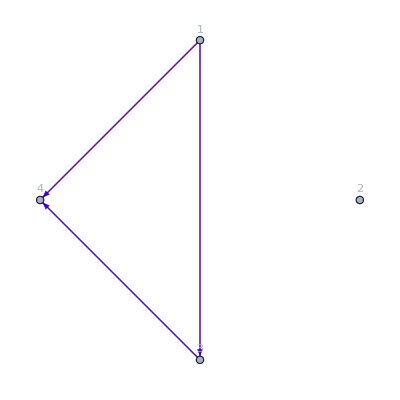
Graphs before momentum conservation:  {-Graphics-}

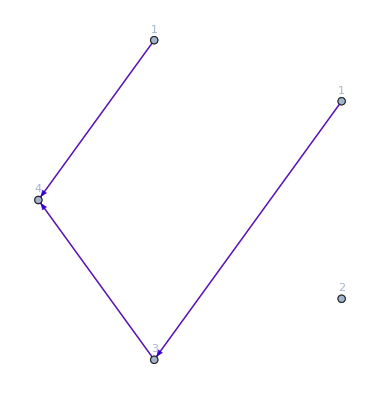
Graphs with momenta:  {-Graphics-}

Conditions:  {True,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,0,0}

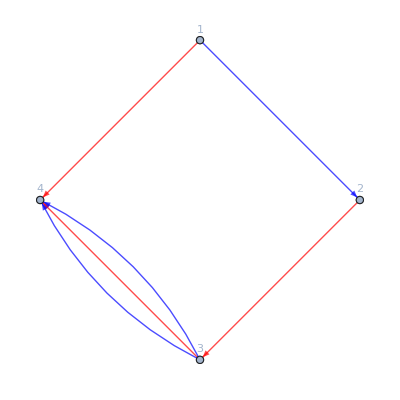
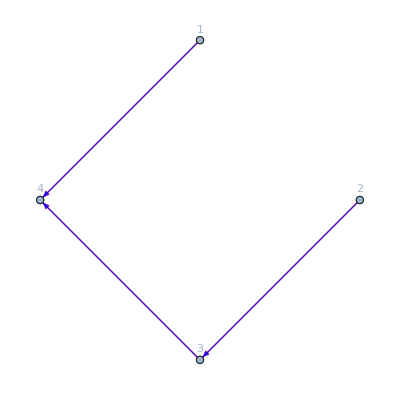
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

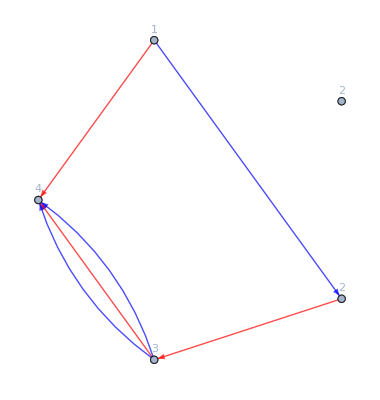
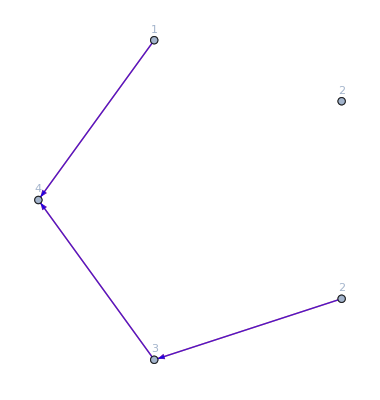
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Momenta:  {0,0,1,0}

Graphs before momentum conservation:  {-Graphics-}

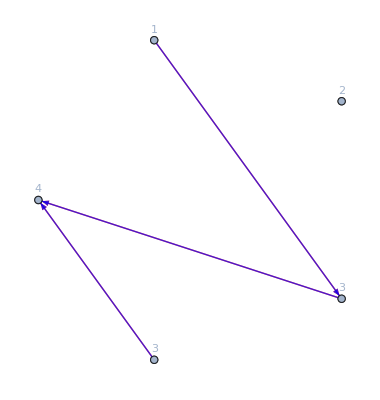
Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

4

Momenta:  {1,0,0,0}

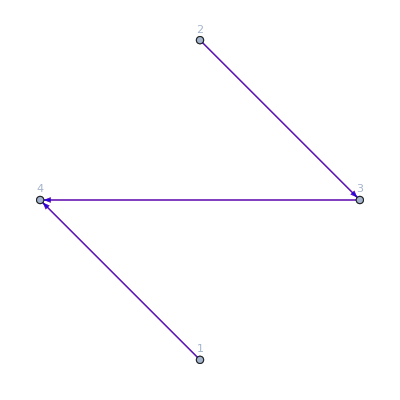
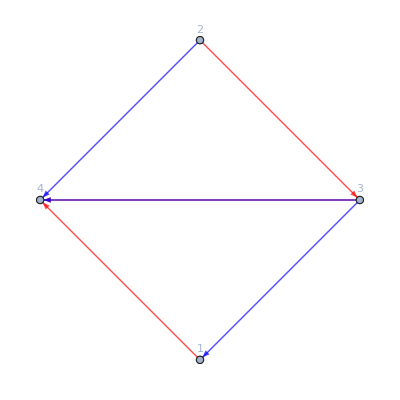
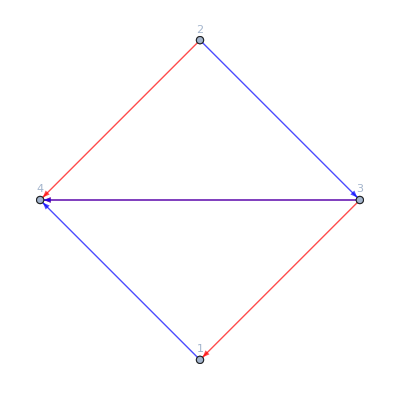
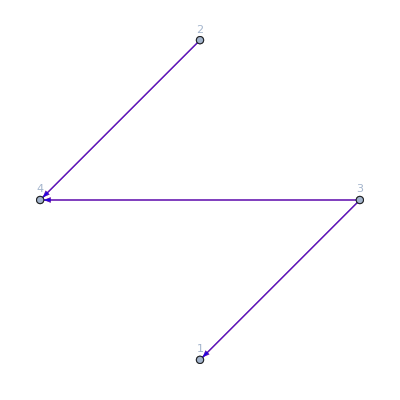
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

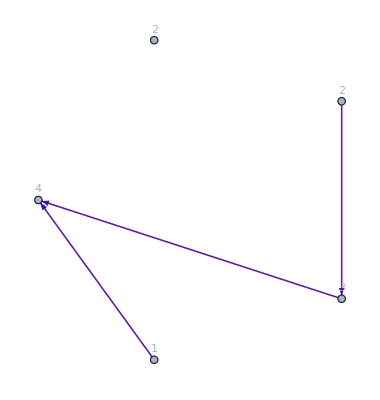
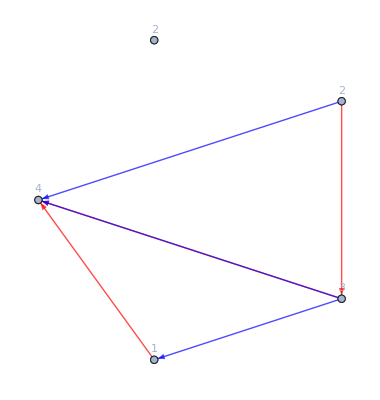
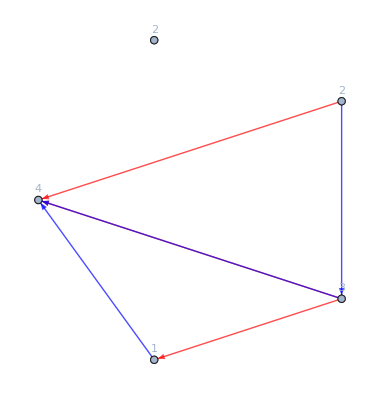
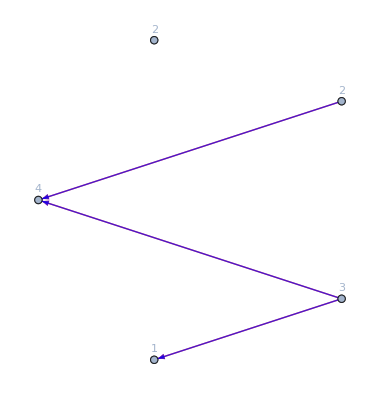
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

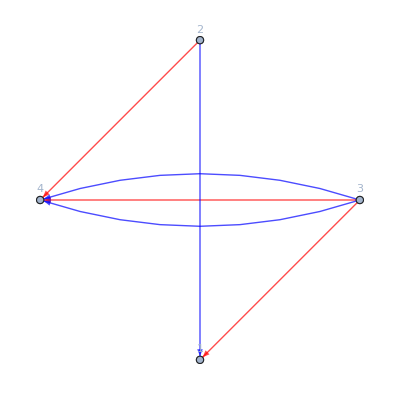
Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-,-Graphics-}

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,1,0,0}

Graphs before momentum conservation:  {-Graphics-}

Graphs with momenta:  {-Graphics-}

Conditions:  {}

False

Graphs:  {-Graphics-}

Momenta:  {0,0,1,0}

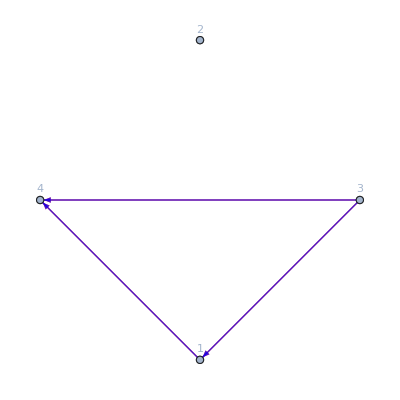
Graphs before momentum conservation:  {-Graphics-}

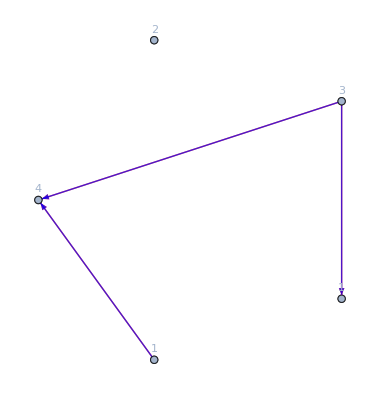
Graphs with momenta:  {-Graphics-}

Conditions:  {True}

True

No graph survided.

3

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{3,2,0},{1,1,0},{4,2,0},{2,0,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,0,0},{3,2,0},{4,2,0}]//Length
UniformMassStructres[6,"MomentumConservation"->True,"Echos"->True][{2,0,0},{3,2,0},{1,1,0},{4,2,0}]//Length
```

```mathematica
If[Length[UniformMassStructres[10,"MomentumConservation"->True][Sequence@@#]]==10,#,Nothing]&/@Permutations[{{1,1,0},{2,1,0},{3,2,0},{4,2,0}}]
```

{}

```mathematica
UniformMassStructres[10,"MomentumConservation"->True][{1,2,0},{2,1},{3,1,0},{4,1},{5,2}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2},{3,1},{4,2,0},{5,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1},{2,2,0},{3,1,0},{4,1},{5,2}]//Length
```

47

47

47

```mathematica
UniformMassStructres[6,"MomentumConservation"->True][{1,1,0},{2,2,0},{3,1,0},{a,1,0},{b,2},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,2,0},{3,1,0},{a,1,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,1,0},{3,1,0},{a,2,0},{b,1,0},{4,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,2,0},{b,1,0},{4,1,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,2},{2,0},{3,1,0},{a,1,0},{b,1,0},{4,2,0}]//Length
UniformMassStructres[10,"MomentumConservation"->True][{1,1,0},{2,0},{3,1,0},{a,2},{b,1,0},{4,2,0}]//Length
```

0

240

240

240

«1 more identical outputs»

236

```mathematica
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,2,1},{3,1,0},{4,0}]//Length
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,2,1},{3,0},{4,1,0}]//Length
UniformMassStructres[13,"MomentumConservation"->True][{1,1,0},{2,0},{3,2,1},{4,1,0}]//Length
```

6

6

6

```mathematica
UniformMassStructres[8,"MomentumConservation"->True][{1,1},{2,1,1},{3,1,0},{4,1,1},{5,1}]//Length
UniformMassStructres[8,"MomentumConservation"->True(*,"Echos"->True*)][{1,1,1},{2,1},{3,1},{4,1,1},{5,1,0}]//Length
```

39

39

```mathematica
UniformMassStructres[9,"MomentumConservation"->True][{1,2},{2,1},{3,1},{4,1},{5,1},{6,2},{7,1}]//Length
UniformMassStructres[9,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2},{5,1},{6,1},{7,2}]//Length
```

50

50

```mathematica
Length/@(UniformMassStructres[21,"MomentumConservation"->True][Sequence@@#]&/@(Permutations[{{1,2,1},{2,1,0},{3,1,0},{4,1,0}}]))
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

Momenta:  {0,2,0,0}

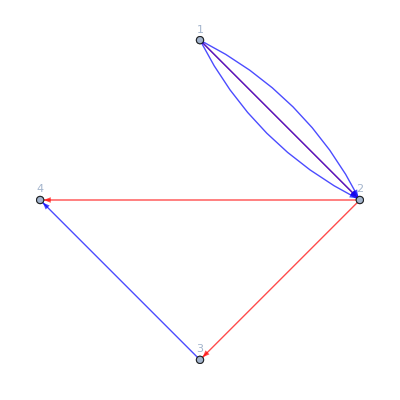
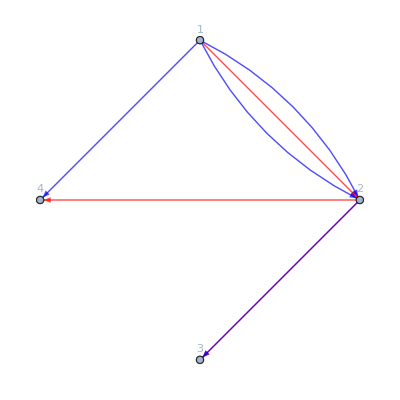
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

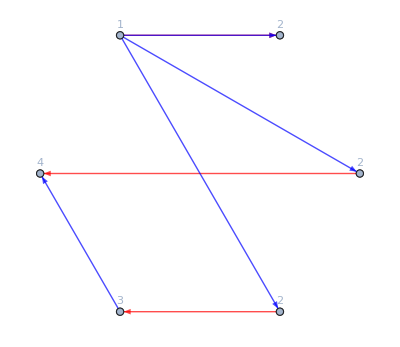
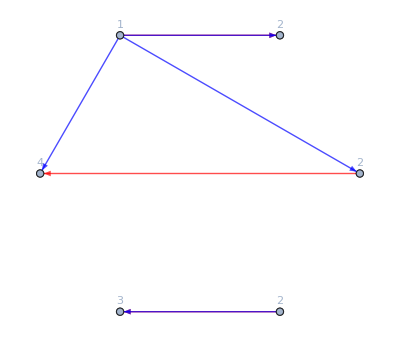
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

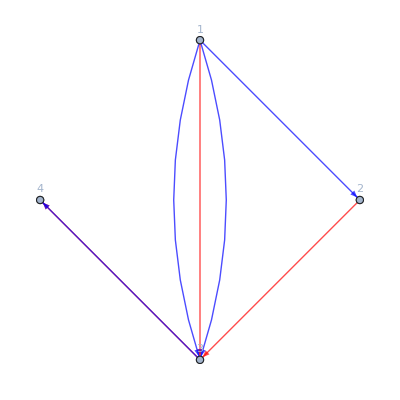
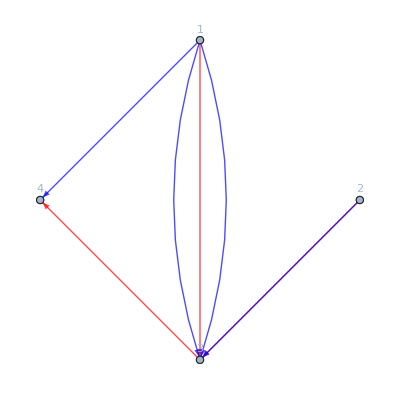
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

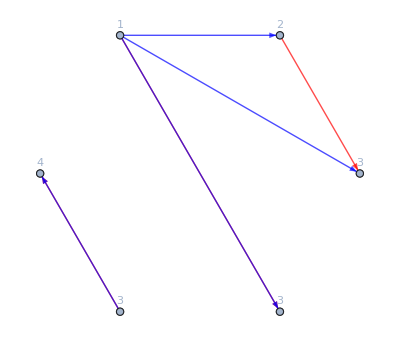
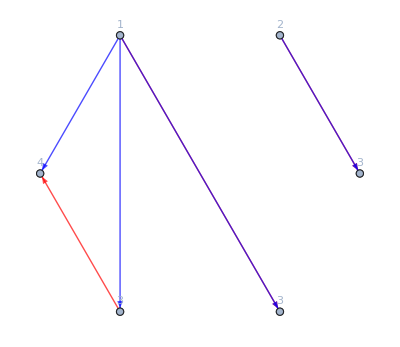
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

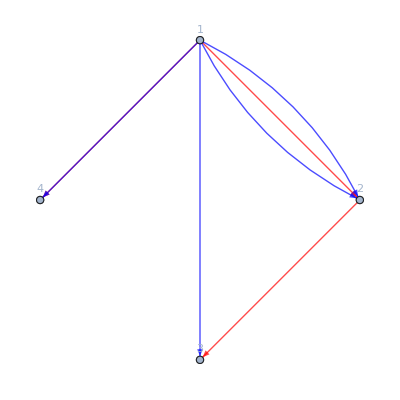
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

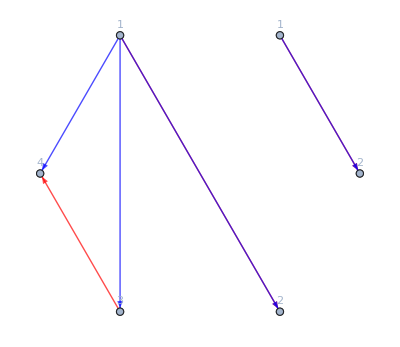
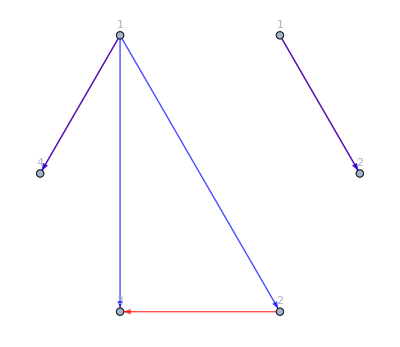
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,True}

True

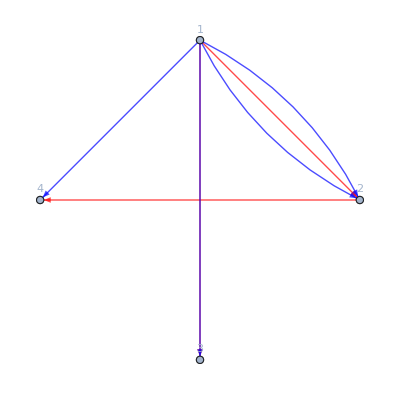
Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-}

No graph survided.

Momenta:  {1,0,1,0}

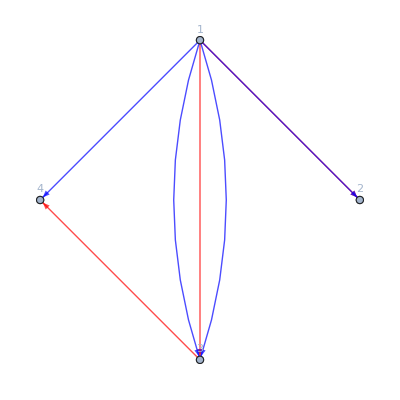
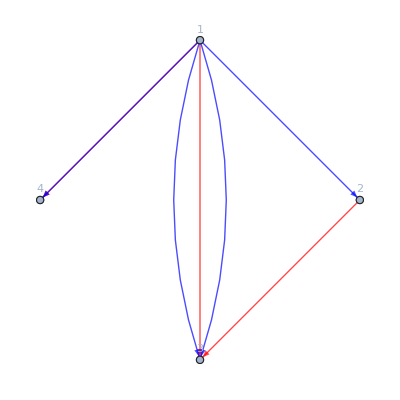
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

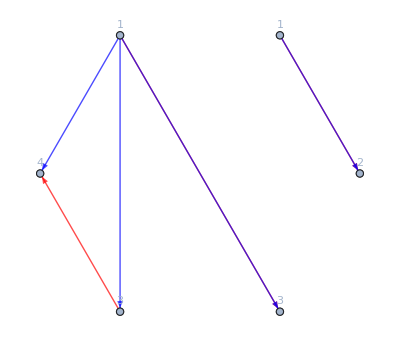
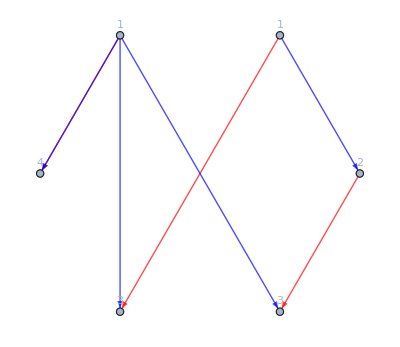
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,True,False,True}

True

Conditions:  {False,True,True,True}

True

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,1,0}

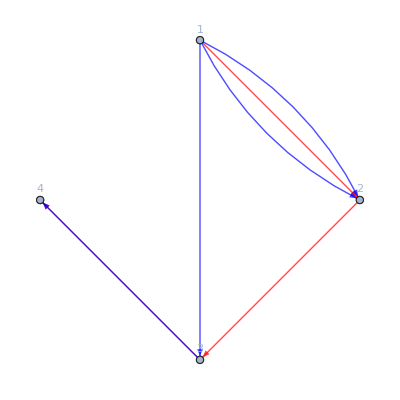
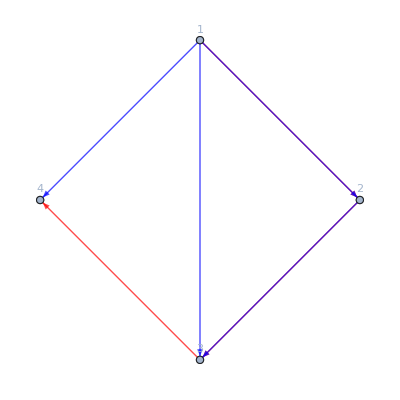
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

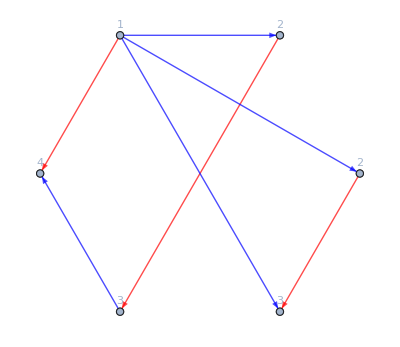
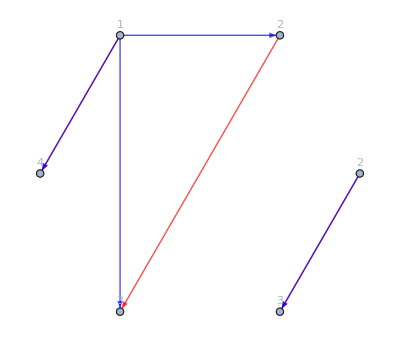
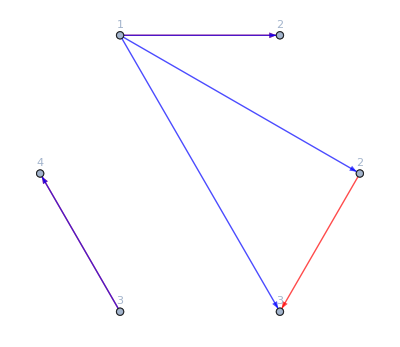
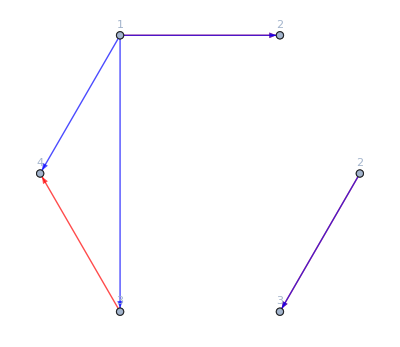
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {False}

False

Conditions:  {True}

True

Conditions:  {True}

True

Graphs:  {-Graphics-}

3

Momenta:  {2,0,0,0}

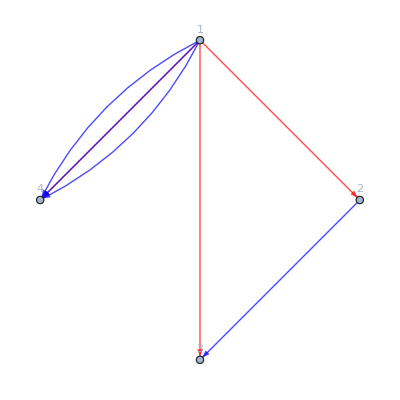
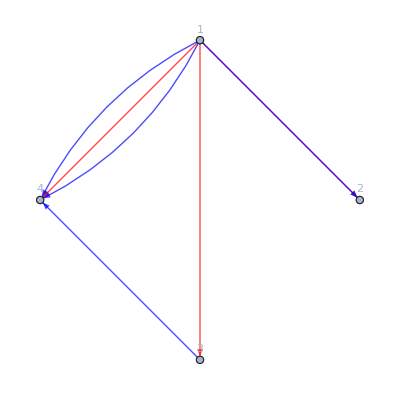
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

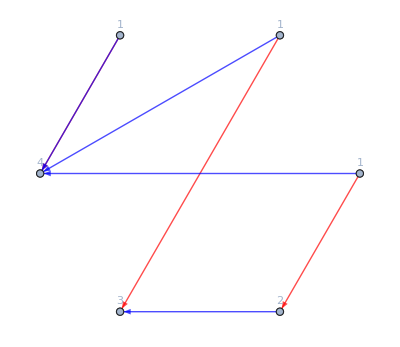
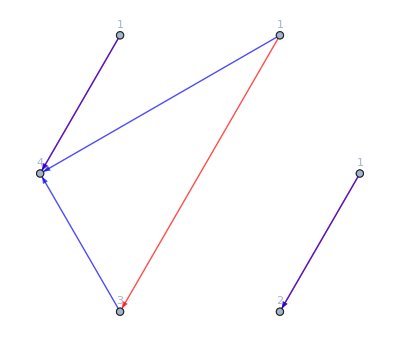
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True,False}

True

Conditions:  {True,False}

True

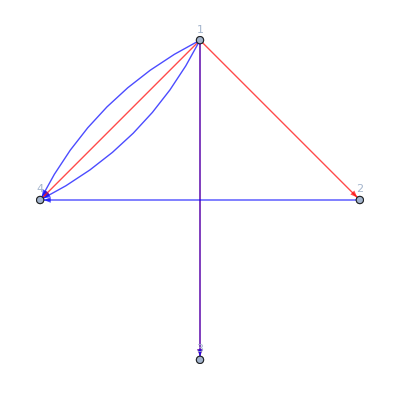
Extra momentum conservatin:  {-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-}

No graph survided.

Momenta:  {0,2,0,0}

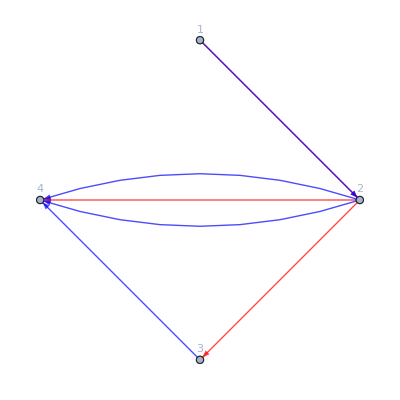
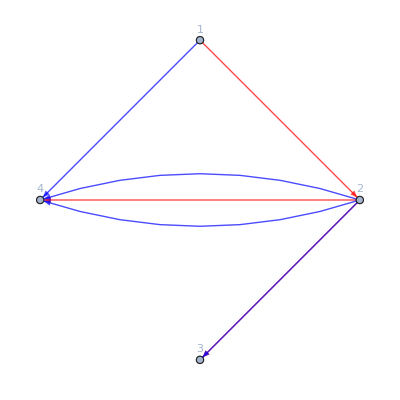
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

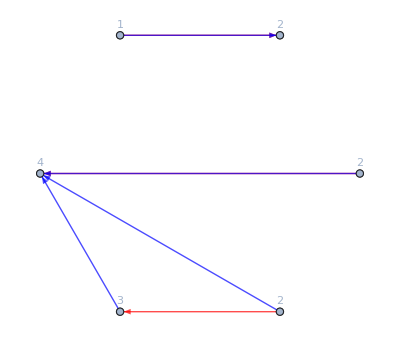
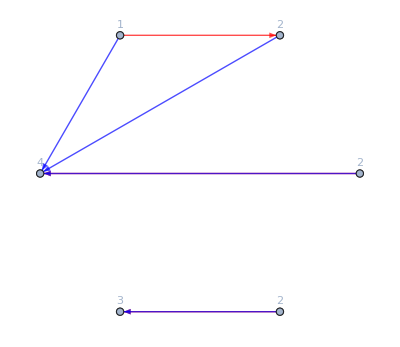
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {}

False

Conditions:  {}

False

Graphs:  {-Graphics-,-Graphics-}

Momenta:  {0,0,2,0}

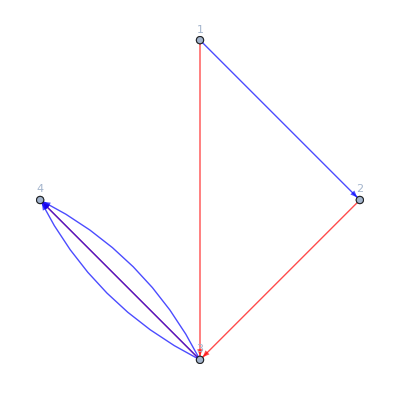
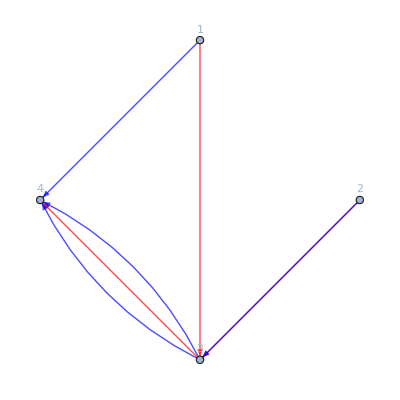
Graphs before momentum conservation:  {-Graphics-,-Graphics-}

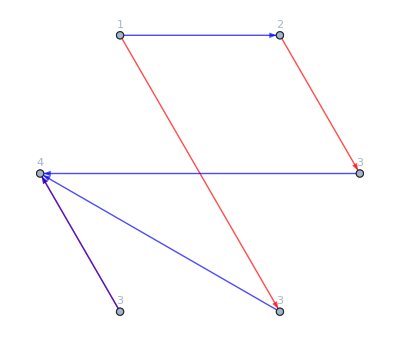
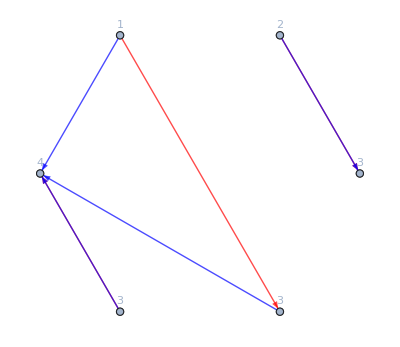
Graphs with momenta:  {-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

Momenta:  {1,1,0,0}

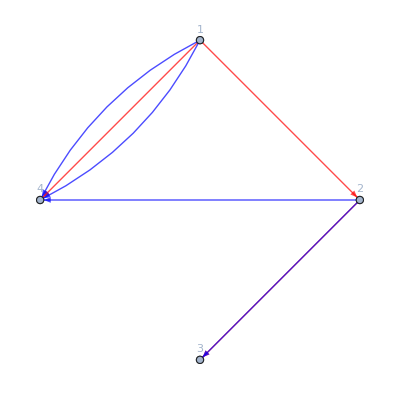
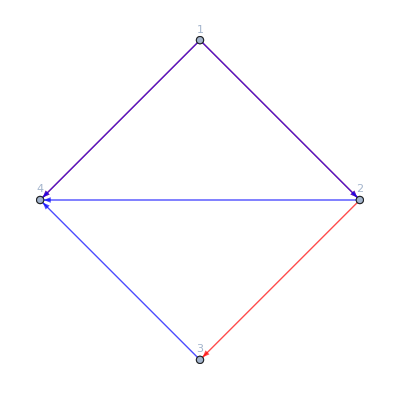
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

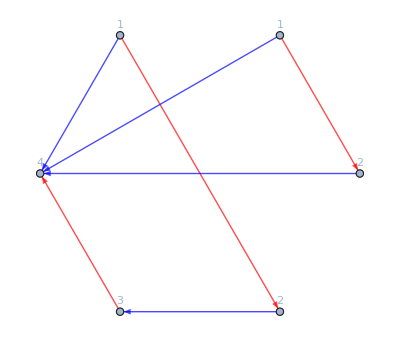
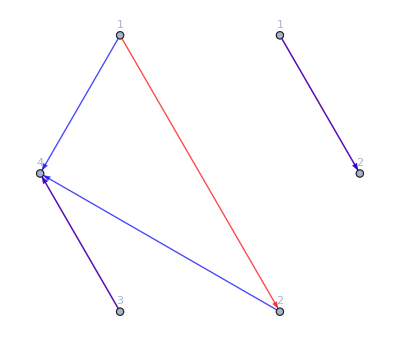
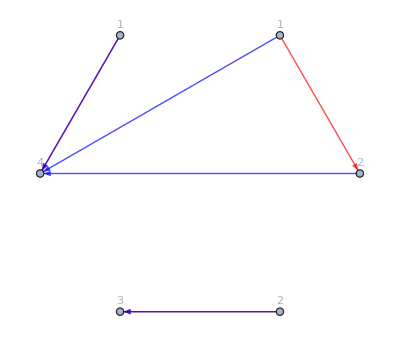
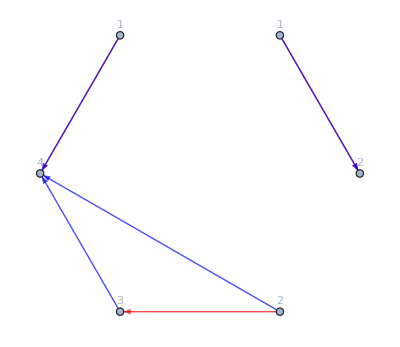
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

Conditions:  {False,False}

False

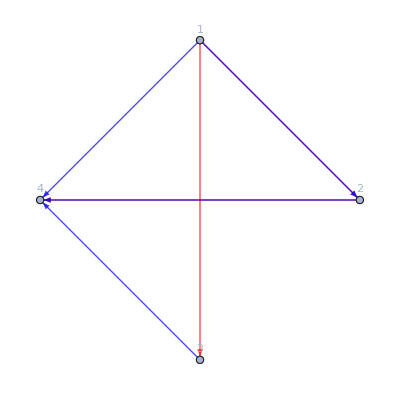
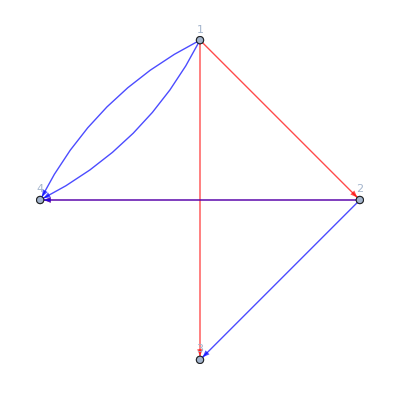
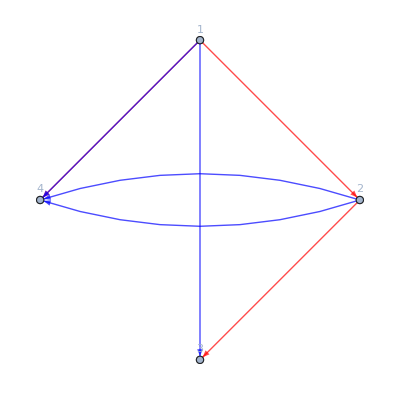
Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Extra momentum conservatin:  {-Graphics-,-Graphics-,-Graphics-}

Graphs:  {-Graphics-}

Momenta:  {1,0,1,0}

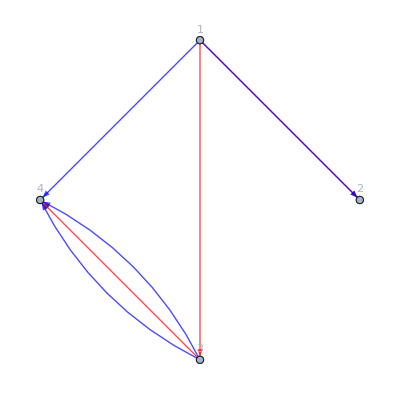
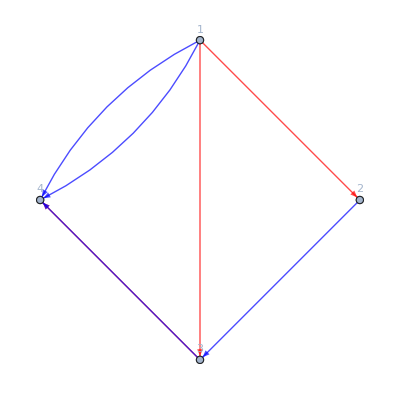
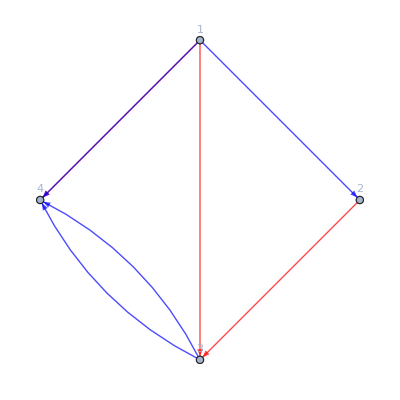
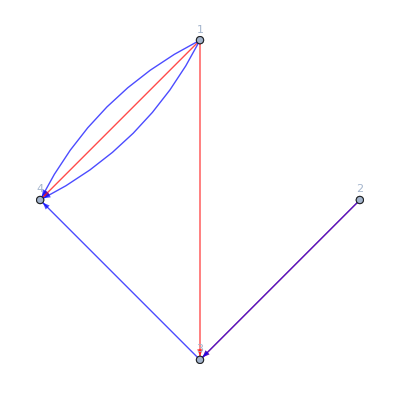
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

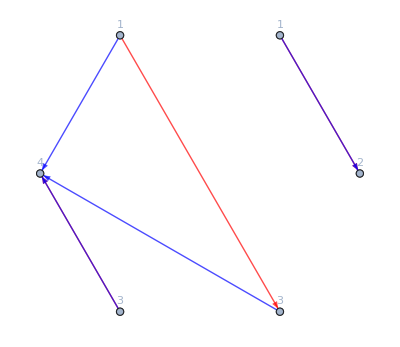
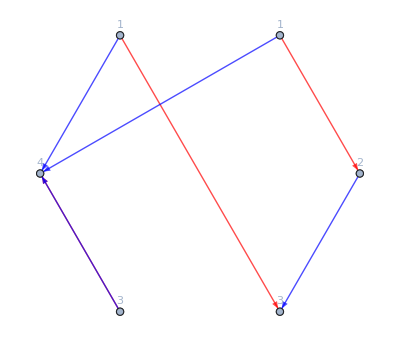
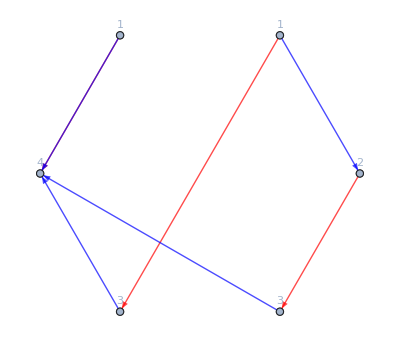
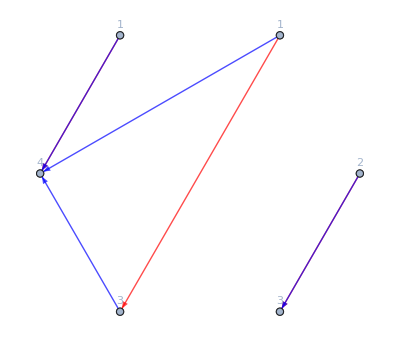
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Conditions:  {True,True,False,False}

True

Extra momentum conservatin:  {}

Extra momentum conservatin:  {}

No graph survided.

Momenta:  {0,1,1,0}

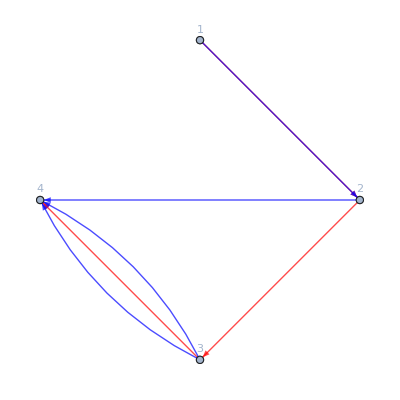
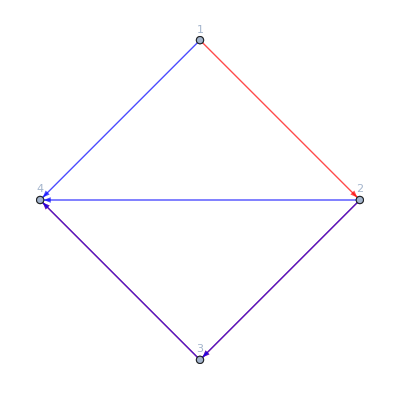
Graphs before momentum conservation:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

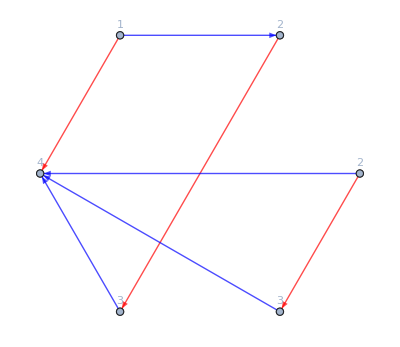
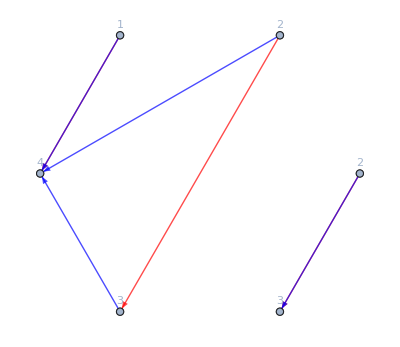
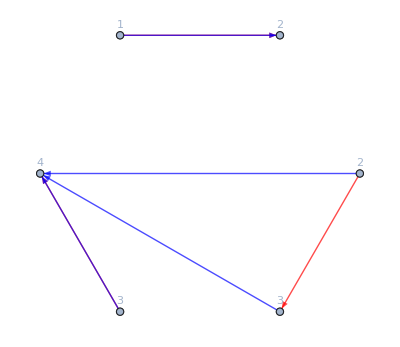
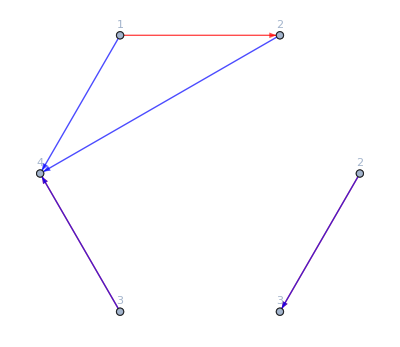
Graphs with momenta:  {-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

Conditions:  {True}

True

No graph survided.

3

```mathematica
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,2,1},{2,1,0},{3,1,0},{4,1,0}]//Length
UniformMassStructres[7,"MomentumConservation"->True,"Echos"->True][{1,1,0},{2,1,0},{3,1,0},{4,2,1}]//Length
```

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,2,0},{2,1},{3,1},{4,1}]
(*UniformMassStructres[6,"MomentumConservation"->True][{4,2,1},{2,1},{3,1},{1,1}]
UniformMassStructres[5,"MomentumConservation"->True][{4,2,2},{2,1},{3,1},{1,1}]
UniformMassStructres[6,"MomentumConservation"->True][{4,2,-1},{2,1},{3,1},{1,1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{4,2,-2},{2,1},{3,1},{1,1}]//Length*)
```

{21^2 23 24 21^2 34,21^2 23^2 24 21 41,21 31 23^3 41^2}

```mathematica
UniformMassStructres[7,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,0}]
(*UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,1}]
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,2}]
UniformMassStructres[6,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-1}]//Length
UniformMassStructres[5,"MomentumConservation"->True][{1,1},{2,1},{3,1},{4,2,-2}]//Length*)
```

{24^2 12^2 23 24 34,24^2 12 14 23^2 24,14 24 12^2 14 23 34}

```mathematica
IndependentSpinStructres [7,"MomentumConservation"->True][{1,1},{2,1,0},{3,1,0},{4,0,0}]
```

{-12 11p_2 31p_2 12 13,-21p_3 33p_2 2I232I23p_3 12,12 33p_2 12 11p_2p_3,-(21p_3)^2 33p_2 2,-12 21p_3 31p_2 2 13,-13 11p_2 2 12^2 13,11p_2 33p_2 2 12^2,33p_2 2I232I23p_3 2 12^2,12 (31p_2)^2 3 12,-23p_3p_2 31p_2 3 12,-12 11p_2 3 12 13^2,21p_3 3 23 13p_3p_2,-12 3 12 13 13p_3p_2,-23 21p_3 31p_2 2 3,-12 21p_3 2 3 13^2,13 31p_2 2 3 12^2,13p_2 2 3 12^2 13,-2 3 12 23 13p_3p_2}